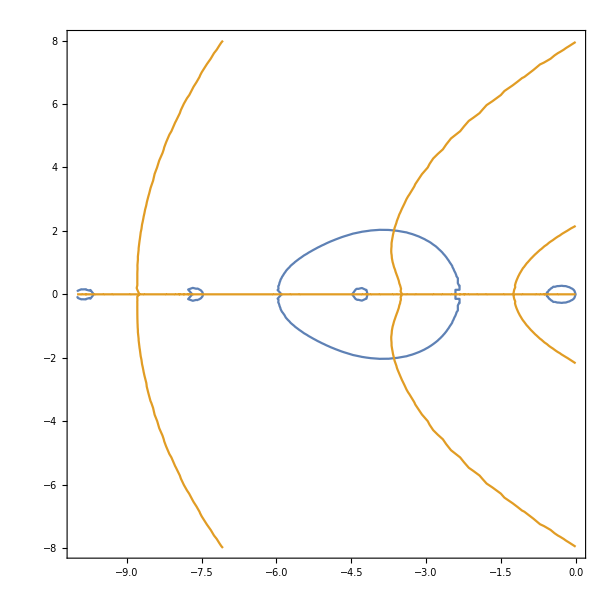

Reduce::inex: Reduce was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Reduce require exact input, providing Reduce with an exact version of the system may help.

Reduce[(4.48169 ParabolicCylinderD[-a-ⅈ b,2.52982])/ParabolicCylinderD[-a-ⅈ b,-0.632456]==1&&-16<a<0&&-11<b<11,{a,b}]

-Graphics3D-

-Graphics3D-

```mathematica
δ=(vr^2-vt^2+2 μ (vt-vr))/(4 d);
(*Laplace transform of ISI density*)
λ=a+I*b;
param={μ->0.8,vr->0,vt->1,d->0.1};PL=Exp[δ] ParabolicCylinderD[-λ,(μ-vr)/Sqrt[d]]/ParabolicCylinderD[-λ,(μ-vt)/Sqrt[d]]/.param;



ContourPlot[{Re[PL]==1,Im[PL]==0,0},{a,-10,0},{b,-8,8}]

Reduce[PL==1 && -16<a<0 &&-11<b<11,{a,b}]

Plot3D[Re[PL-1],{a,-2,0},{b,-1,1}]
Plot3D[Im[PL-1],{a,-1,0},{b,-1,1}]
```

```mathematica
f=(PL-1)/λ;
Plot3D[{Re[(PL-1)],Im[(PL-1)],0},{a,-5,0},{b,-10,10}]
Plot3D[{Re[f],Im[f],0},{a,-5,0},{b,-10,10}]
(*Plot3D[Im[f],{a,-1,0},{b,-1,1}]*)
```

-Graphics3D-

-Graphics3D-

```mathematica
finv=1/f;
Plot3D[{Re[finv],Im[finv]},{a,-5,0},{b,-10,10}]
```

-Graphics3D-

```mathematica
PisiL=Exp[δ] ParabolicCylinderD[-s,(μ-vr)/Sqrt[d]]/ParabolicCylinderD[-s,(μ-vt)/Sqrt[d]];
Finv=s/(PisiL-1);
g=Normal[Simplify[Series[Finv,{s,0,1}]]]
```

-((ⅇ^(-((vr-vt) (vr+vt-2 μ))/(4 d)) ParabolicCylinderD[0,(-vt+μ)/(√d)]^2)/(ParabolicCylinderD[0,(-vt+μ)/(√d)] ParabolicCylinderD^(1,0)[0,(-vr+μ)/(√d)]-ParabolicCylinderD[0,(-vr+μ)/(√d)] ParabolicCylinderD^(1,0)[0,(-vt+μ)/(√d)]))-(ⅇ^(-((vr-vt) (vr+vt-2 μ))/(4 d)) s ParabolicCylinderD[0,(-vt+μ)/(√d)] (2 ParabolicCylinderD[0,(-vr+μ)/(√d)] (ParabolicCylinderD^(1,0)[0,(-vt+μ)/(√d)])^2+ParabolicCylinderD[0,(-vt+μ)/(√d)]^2 ParabolicCylinderD^(2,0)[0,(-vr+μ)/(√d)]-ParabolicCylinderD[0,(-vt+μ)/(√d)] (2 ParabolicCylinderD^(1,0)[0,(-vr+μ)/(√d)] ParabolicCylinderD^(1,0)[0,(-vt+μ)/(√d)]+ParabolicCylinderD[0,(-vr+μ)/(√d)] ParabolicCylinderD^(2,0)[0,(-vt+μ)/(√d)])))/(2 (ParabolicCylinderD[0,(-vt+μ)/(√d)] ParabolicCylinderD^(1,0)[0,(-vr+μ)/(√d)]-ParabolicCylinderD[0,(-vr+μ)/(√d)] ParabolicCylinderD^(1,0)[0,(-vt+μ)/(√d)])^2)

```mathematica
Papprox=Simplify[1+s/g];
Papproxplot=Papprox/.param;
Plot3D[Re[Papproxplot/.{s->a+I*b}],{a,-1,0},{b,-1,1}]
Plot3D[Im[Papproxplot/.{s->a+I*b}],{a,-1,0},{b,-1,1}]
```

-Graphics3D-

-Graphics3D-